```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
$K = 9;
Do[
data[$N] = ToExpression@Import["../../../runs/Stats-Moments-2/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
, {$N, 3, 9}];
```

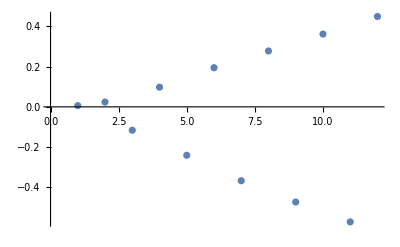

```mathematica
ListPlot[((#["Uncertainty"])/(#["Value"]))&/@Around/@(data[9][[All, 2;;]]ᵀ)]
```

```mathematica
Do[
α[$N] = ($K(($N)^2-1))/($N Mean@data[$N][[All, 2]]);
, {$N, 3, 9}]
```

```mathematica
ClearAll[mom]
```

```mathematica
Do[
mom[n, r] = CentralMoment[#, r]/StandardDeviation[#]^r&@GammaDistribution[($K(n^2-1))/2, 2/(α[n] n)];
,{n, 3, 9}, {r, 3, 12}];
```